```mathematica
(* RUN transientQBD_functions.nb FIRST !!!! *)
D0=({{-8, 1, 3}, {0, -6, 4}, {2, 0, -3}}); D1=({{3, 1, 0}, {0, 2, 0}, {0, 0, 1}});S0=({{-3, 1}, {6, -7}});S1=({{0, 2}, {1, 0}});
(D0+D1).{1,1,1};
(S0+S1).{1,1};
(* arrival rate *)
CTMCSolve[D0+D1].D1.{1,1,1}//N
(* service rate *)
CTMCSolve[S0+S1].S1.{1,1}//N
pi=KroneckerProduct[{CTMCSolve[D0+D1]},{CTMCSolve[S0+S1]}][[1]]
```

1.875

1.7

{7/40,3/40,7/80,3/80,7/16,3/16}

```mathematica
I3=IdentityMatrix[3];
I2=IdentityMatrix[2];
mLv=KroneckerProduct[D0,I2];
mL=KroneckerProduct[D0,I2]+KroneckerProduct[I3,S0];
mF=KroneckerProduct[D1,I2];
mB=KroneckerProduct[I3,S1];
```

```mathematica
Tfinite={0,1,39, 40, 80};
Tinfinite={0,1,39, 40};
K = 4;

F=ConstantArray[0,K];
B=ConstantArray[0,K];
L=ConstantArray[0,K];
Lv=ConstantArray[0,K+1];

Lv[[1]]=mLv;
F[[1]]=Table[0,{6},{12}];
F[[1,1;;6,1;;6]]=mF;
B[[1]]=Table[0,{12},{6}];
B[[1,7;;12,1;;6]]=mB;
```

```mathematica
Lv[[2]]=Table[0,{12},{12}];
Lv[[2,1;;6,1;;6]]=mLv;
Lv[[2,7;;12,7;;12]]=mL;
L[[2]]=Lv[[2]];
F[[2]]=Table[0,{12},{12}];
F[[2,1;;6,1;;6]]=mF;
F[[2,7;;12,7;;12]]=mF;
B[[2]]=Table[0,{12},{12}];
B[[2,7;;12,7;;12]]=mB;
```

```mathematica
Lv[[3]]=Lv[[2]];
F[[3]]=Table[0,{12},{6}];
F[[3,1;;6,1;;6]]=mF;
F[[3,7;;12,1;;6]]=mF;
B[[3]]=Table[0,{6},{12}];
B[[3,1;;6,7;;12]]=mB;
```

```mathematica
Lv[[4]]=mL;
L[[4]]=mL;
F[[4]]=mF;
B[[4]]=mB;

Lv[[5]]=mL+mF;
```

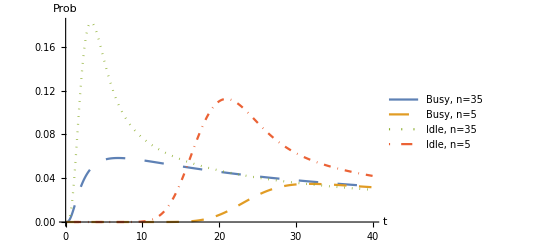

```mathematica
(* Initial Vector Definition *)
pilow=Table[0,{12}];
pilow[[1;;6]]=pi;
pihigh=Table[0,{12}];
pihigh[[7;;12]]=pi;

n2=5;
n=35;
m=40;
tt=40;  (* Time limit *)
(* Inverse Laplace Transformation for n=5,35 *)
res= ILT[Function[s,Transient2Open[B,L,F,Lv,Tinfinite,n,m,s]],Range[1/10,tt,1/10], 35];
res2= ILT[Function[s,Transient2Open[B,L,F,Lv,Tinfinite,n2,m,s]  ],Range[1/10,tt,1/10], 35];

(* PiHigh*Transient Prob n=5,35 *)
fresHigh=Table[Total[pihigh.res[[i,;;,;;]]],{i,1,Dimensions[res][[1]]}];
line=Transpose[{Range[1/10,tt,1/10],fresHigh}];
fresHigh2=Table[Total[pihigh.res2[[i,;;,;;]]],{i,1,Dimensions[res2][[1]]}];
line2=Transpose[{Range[1/10,tt,1/10],fresHigh2}];

(* PiLow*Transient Prob for n=5,35 *)
fresLow=Table[Total[pilow.res[[i,;;,;;]]],{i,1,Dimensions[res][[1]]}];
line3=Transpose[{Range[1/10,tt,1/10],fresLow}];
fresLow2=Table[Total[pilow.res2[[i,;;,;;]]],{i,1,Dimensions[res2][[1]]}];
line4=Transpose[{Range[1/10,tt,1/10],fresLow2}];
(* plot the result *)
ListLinePlot[{line,line2,line3,line4},PlotRange->All,PlotLegends->Placed[{"Busy, n=35","Busy, n=5", "Idle, n=35","Idle, n=5"},{Right,Top}],AxesLabel->{"t","Prob"},PlotStyle -> { Dashing[Large],Dashing[Medium], Dotted,DotDashed}]
```